```mathematica
AB=l1=93.75;
BC=l2=421.875;
h=187.5;
α=0.22409309230137084;
CD=l3=195.;
ls2=0.3BC;
ls3=0.3BC;
pmax=8 10^5;
pmin=-8 10^4;
m2=12;
m3=7.8;
Js2=0.214;
Js1=0.025;
iSize=400;
d4=0.05;
d3=0.018;
g=9.81;
n1=1.6;
w1sr=2Pi n1;
δ=1/20;
opt=AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}};
```

```mathematica
phi2[x_]:=ArcSin[-l1/l2 Sin[x]]
Rb[x_]:={AB Cos[x],AB Sin[x],0}
Rc[x_]:={AB Cos[x]+BC Cos[phi2[x]],AB Sin[x]+BC Sin[phi2[x]],0}
Rd[x_]:=Rc[x]+{CD,0,0}
Rs2[x_]:={AB Cos[x]+ls2  Cos[phi2[x]],AB Sin[x]+ls2 Sin[phi2[x]],0}
Rs3[x_]:=Rc[x]+{ls3,0,0}
```

```mathematica
Animate[

pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];

Graphics[
{Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],
Point[pS2],Point[pS3],
Line[{pD-{0,100},pD+{0,100},pD+{60,100},pD+{60,-100},pD-{0,100}}],
Circle[#,5]&/@{pA,pB,pC},


FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


},
Axes->False,PlotRange->{{-AB-5,AB+BC+CD+75},{-AB-50,AB+50}}],

{ϕ,0,4Pi}]
```

```mathematica
Vb[x_]:=(D[Rb[y],y]/.y->x)[[1;;2]]
Vc[x_]:=(D[Rc[y],y]/.y->x)[[1;;2]]
Vd[x_]:=(D[Rd[y],y]/.y->x)[[1;;2]]
Vs3[x_]:=(D[Rs3[y],y]/.y->x)[[1;;2]]
Vs2[x_]:=(D[Rs2[y],y]/.y->x)[[1;;2]]
```

```mathematica
Vb[1]
```

{-78.8879,50.6533}

```mathematica
7.8*0.6^2/2
```

1.404

```mathematica
ab[x_]:=(D[Rb[y],{y,2}]/.y->x)[[1;;2]]
ac[x_]:=(D[Rc[y],{y,2}]/.y->x)[[1;;2]]
ad[x_]:=(D[Rd[y],{y,2}]/.y->x)[[1;;2]]
as3[x_]:=(D[Rs3[y],{y,2}]/.y->x)[[1;;2]]
as2[x_]:=(D[Rs2[y],{y,2}]/.y->x)[[1;;2]]
```

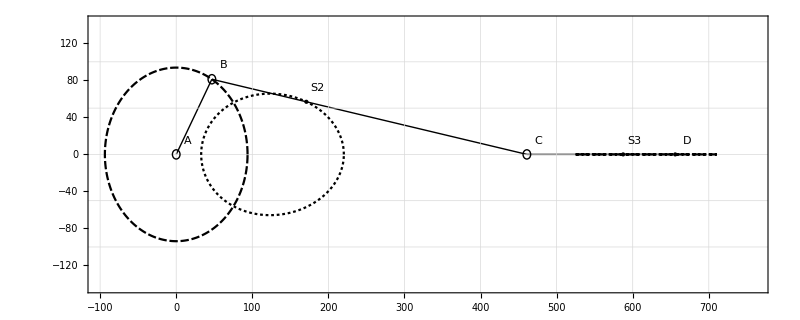

```mathematica
Module[{pA,pB,pC,pD,pS3,pS2,ϕ},
pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];
ϕ=Pi/3;
Show[{Graphics[{PointSize[Large],Thick,Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],Point[pD],Point[pS2],Point[pS3],

Circle[#,5]&/@{pA,pB,pC},
FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


}],
ParametricPlot[{{0,0},Rb[x][[1;;2]],Rs2[x][[1;;2]],Rd[x][[1;;2]]},{x,0,2Pi},PlotTheme->"Monochrome"]
},
Axes->False,Frame->True,GridLines->{Table[100n,{n,-1,10}],Table[50n,{n,-5,5}]},ImageSize->iSize+400,PlotRange->{{-AB-5,AB+BC+CD+50},{-AB-50,AB+50}}]]
```

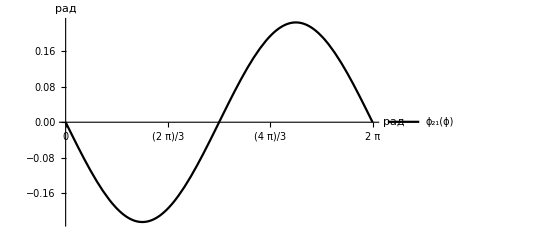

```mathematica
op={Table[Pi /3i,{i,0,8}],Automatic};
Plot[phi2[x],{x,0,2Pi},AxesStyle->Arrowheads[{0.05}],AxesLabel->{"рад","рад"},GridLines->op,Ticks->op,PlotStyle->Black,ImageSize->iSize,PlotLegends->{"ϕ_21(ϕ)"}]
```

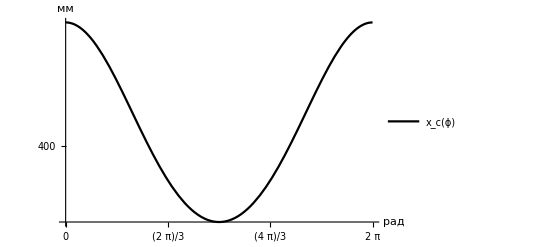

```mathematica
Plot[Rc[x][[1]],{x,0,2Pi},ImageSize->iSize,Ticks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,20}]},AxesStyle->Arrowheads[{0.05}],AxesLabel->{"рад","мм"},GridLines->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,12}]},PlotTheme->"Monochrome",PlotLegends->{"x_c(ϕ)"}]
```

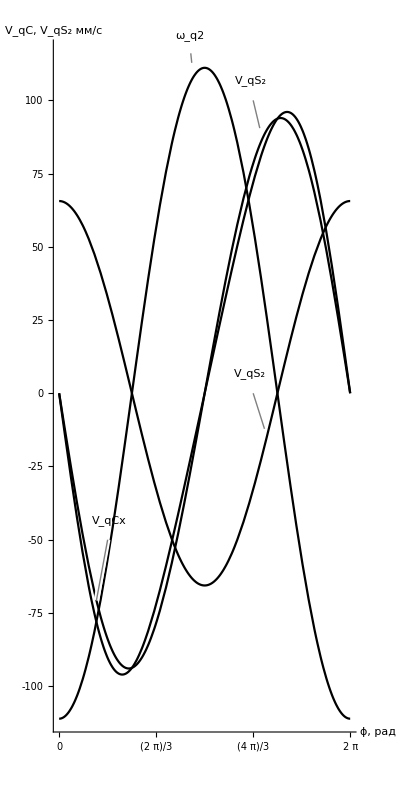

```mathematica
Plot[{Callout[500D[phi2[y],y]/.y->x,"ω_q2",{Pi-0.3,110},Appearance->"Line"],Callout[Vc[x][[1]],"V_qCx",{Pi/3,-50},Appearance->"Line"],Callout[Vs2[x][[1]],"V_qS_2",{4Pi/3,100},Appearance->"Line"],Callout[Vs2[x][[2]],"V_qS_2",{4Pi/3,0},Appearance->"Line"]},{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,8}]},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","V_qC, V_qS_2 мм/c"},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotStyle->Black,AxesOrigin->{0,-125},PlotRange->-130,AspectRatio->2]
```

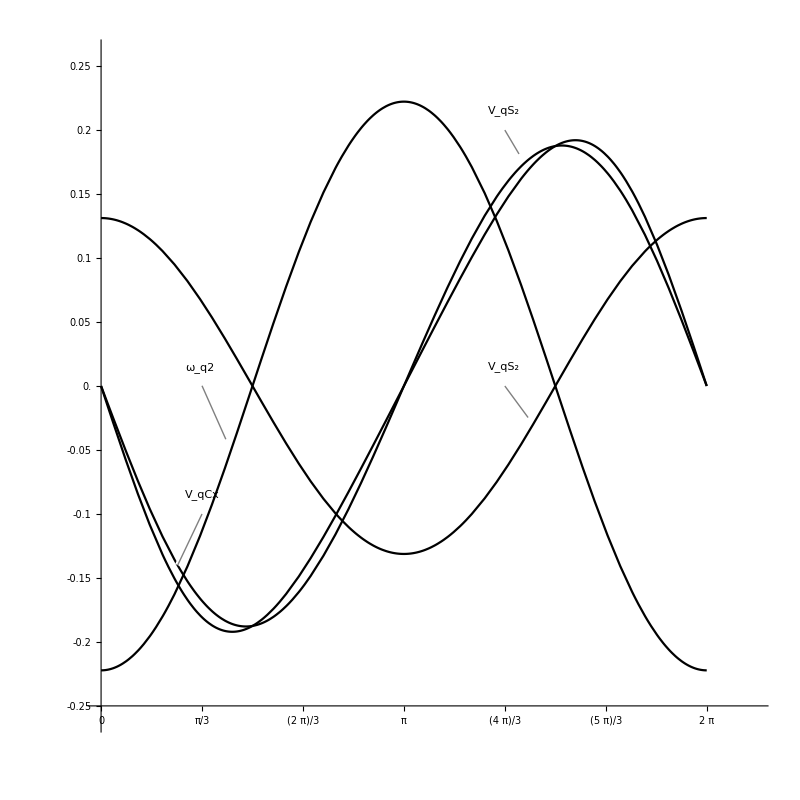

```mathematica
Show[Plot[{Callout[Vc[x][[1]],"V_qCx",{Pi/3,-50},Appearance->"Line"],Callout[Vs2[x][[1]],"V_qS_2",{4Pi/3,100},Appearance->"Line"],Callout[Vs2[x][[2]],"V_qS_2",{4Pi/3,0},Appearance->"Line"]},{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[{25i,25i/500//N},{i,-8,8}]},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->800,PlotStyle->Black,AxesOrigin->{0,-125},PlotRange->{{0,2Pi+0.5},{-130,130}},AspectRatio->1],Plot[Callout[500D[phi2[x],x]/.x->y,"ω_q2",{Pi/3,0.1},Appearance->"Line"],{y,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,100}]},AxesLabel->{"ϕ, рад","ω_q2, 1/c"},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,12}]},ImageSize->iSize,PlotStyle->Black,AxesOrigin->{2Pi/3,-0.3},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AspectRatio->1]]
```

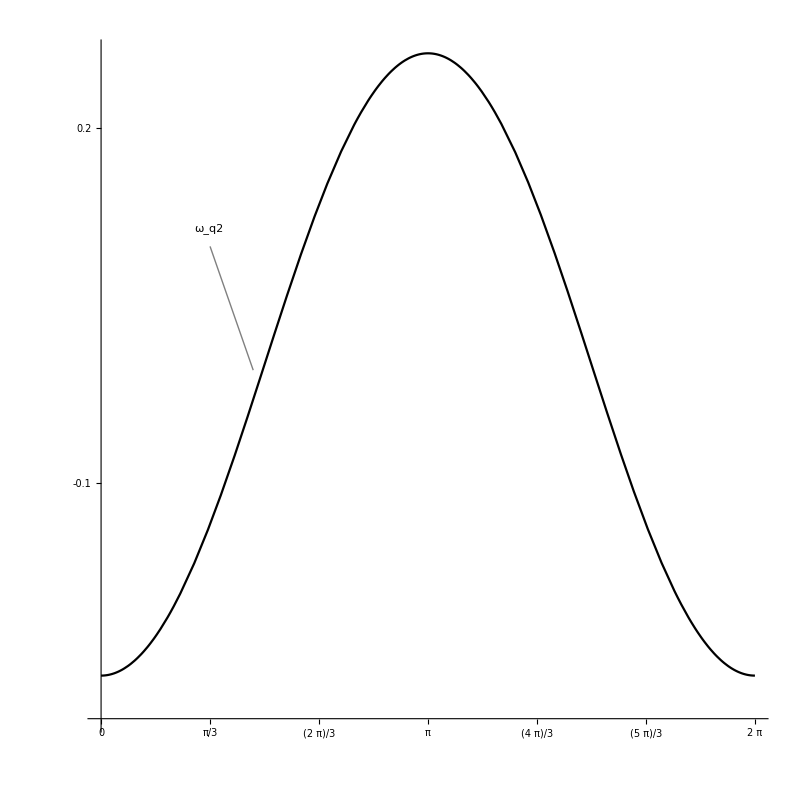

```mathematica
Plot[Callout[D[phi2[x],x]/.x->y,"ω_q2",{Pi/3,0.1},Appearance->"Line"],{y,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,12}]},ImageSize->800,PlotStyle->Black,AxesOrigin->{0,-0.3},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AspectRatio->1]
```

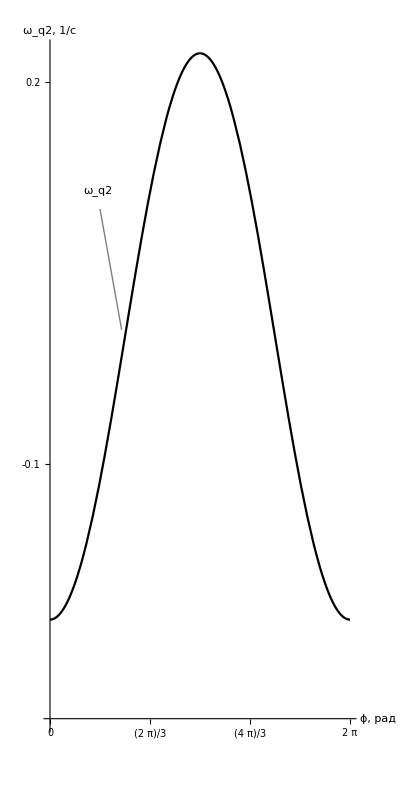

```mathematica
Plot[Callout[1D[phi2[x],x]/.x->y,"ω_q2",{Pi/3,0.1},Appearance->"Line"],{y,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,100}]},AxesLabel->{"ϕ, рад","ω_q2, 1/c"},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,12}]},ImageSize->iSize,PlotStyle->Black,AxesOrigin->{0,-0.3},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AspectRatio->2]
```

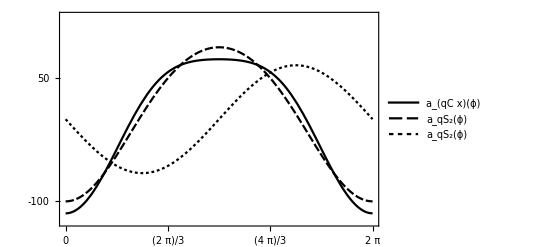

```mathematica
Plot[{ac[x][[1]],as2[x][[1]],as2[x][[2]]},{x,0.001,2Pi-0.001},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,-8,8}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},PlotRange->125,ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"a_(qC x)(ϕ)","a_qS_2(ϕ)","a_qS_2(ϕ)"}]
```

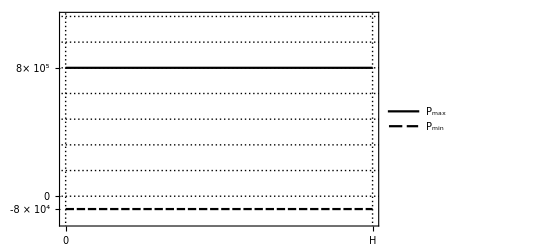

```mathematica
Plot[{10,-1},{x,0,h},Frame->True,GridLines->{{0,h},Table[2i,{i,0,10}]},ExclusionsStyle->Red,FrameTicks->{{0,{h,"H"}},{{-1,"-8 × 10^4"},0,{10,"8× 10^5"}}},PlotRange->{-2,14},PlotTheme->"Monochrome",PlotLegends->{"P_max","P_min"}]
```

```mathematica
Jpr2[x_]:=Js2 (D[phi2[y],y]/.y->x)^2+m2 ((Vs2[x][[1]])^2+(Vs2[x][[2]])^2)/10^6
Jpr3[x_]:=m3 ((Vs3[x][[1]])^2+(Vs3[x][[2]])^2)/10^6
JprII[x_]:=Jpr2[x]+Jpr3[x]
```

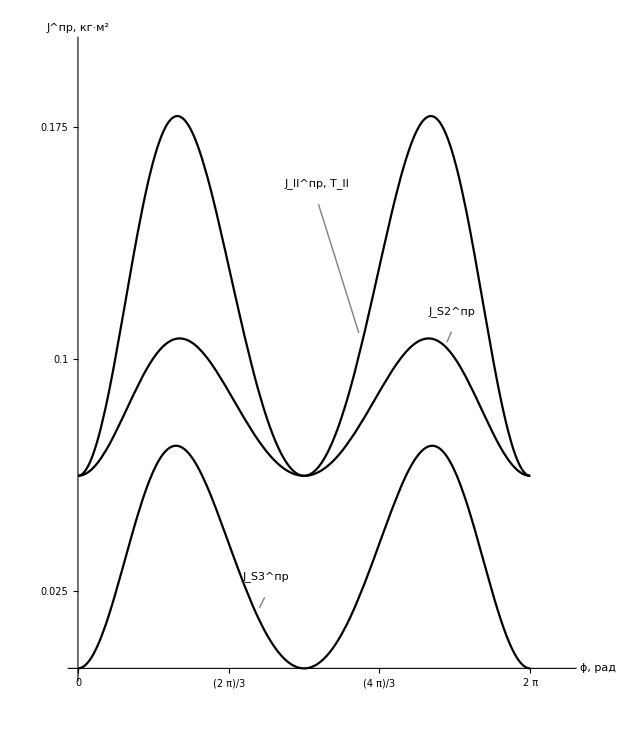

```mathematica
Plot[{Callout[JprII[x],"J_II^(:043f:0440), T_II",{3Pi/3+0.2,0.15},Appearance->"Line"],Callout[Jpr2[x],"J_S2^(:043f:0440)",{4Pi/3+1,0.105},Appearance->"Line"],Callout[Jpr3[x],"J_S3^(:043f:0440)",{2Pi/3+0.5,0.020},Appearance->"Line"]},{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[0.05/2i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.05/2i,{i,-10,12}]},ImageSize->620,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","J^(:043f:0440), кг·(:043c)^2"},AspectRatio->1.2,PlotRange->{{0,2Pi+0.5},{0,0.2}}]
```

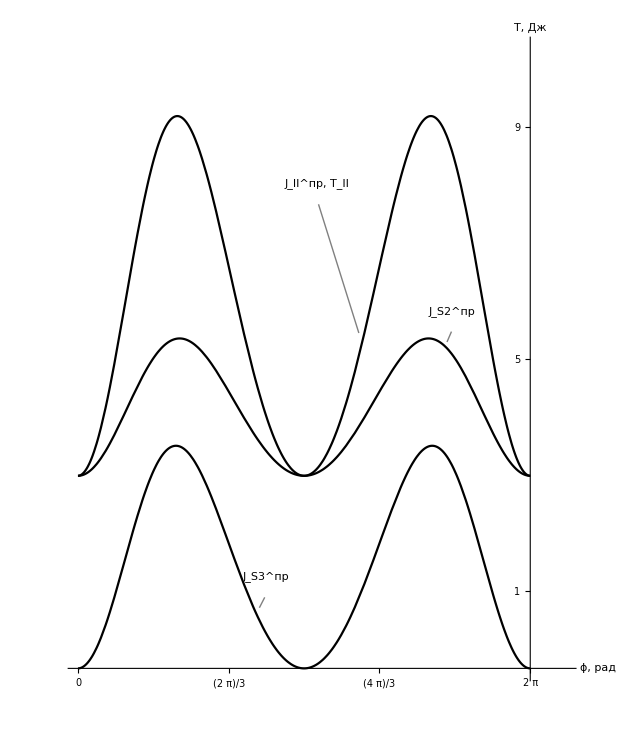

```mathematica
Plot[{Callout[JprII[x],"J_II^(:043f:0440), T_II",{3Pi/3+0.2,0.15},Appearance->"Line"],Callout[Jpr2[x],"J_S2^(:043f:0440)",{4Pi/3+1,0.105},Appearance->"Line"],Callout[Jpr3[x],"J_S3^(:043f:0440)",{2Pi/3+0.5,0.020},Appearance->"Line"]},{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[{0.05/2i,Round[0.05/2i*w1sr^2/2,1]},{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.05/2i,{i,-10,12}]},ImageSize->620,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","T, Дж"},AspectRatio->1.2,PlotRange->{{0,2Pi+0.5},{0,0.2}},AxesOrigin->{2Pi,0}]
```

```mathematica
s[x_]:=Rd[0][[1]]-Rd[x][[1]]
```

```mathematica
p[x_]:=Piecewise[{{pmax,1Pi≤x≤2Pi},{pmin,0≤ x<1Pi}}]
Fc[x_]:=Piecewise[{{-pmax Pi d4^2/4-pmin Pi/4(d4^2-d3^2) ,1Pi≤x≤2Pi},{+pmax Pi/4(d4^2-d3^2)+pmin Pi/4 d4^2,0≤ x<1Pi}}]
```

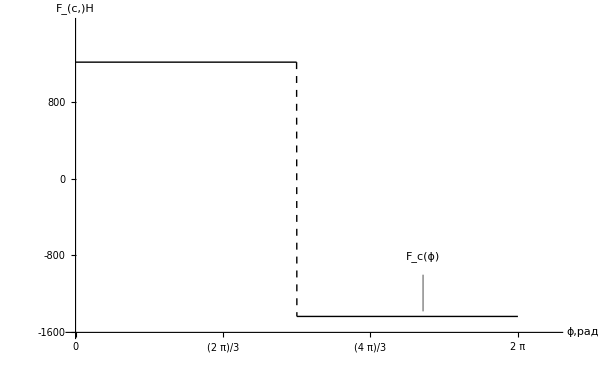

```mathematica
Plot[Callout[Fc[z],"F_c(ϕ)",{5Pi/3-0.3,-1000},Appearance->"Line"],{z,0,2Pi},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ,рад","F_(:0441,)Н"},Ticks->{Table[Pi /3i,{i,0,8}],Table[400i,{i,-8,3}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[400i,{i,-10,4}]},ImageSize->{iSize+200,iSize},PlotStyle->{Black,Thick},ExclusionsStyle->Dashed,AxesOrigin->{0,-1600},PlotRange->{{0,2Pi+0.5},{-1600,1600}}]
```

```mathematica
.
```

```mathematica
Mprc[x_]:={Fc[x],0}. Vc[x]/1000
MprG2[x_]:={0,-m2 g}.Vs2[x]/1000
Mprsopr[x_]:=Mprc[x]+MprG2[x]
```

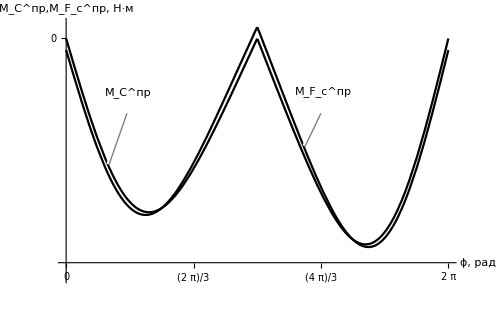

```mathematica
Plot[{Callout[Mprsopr[x],"M_(:0421)^(:043f:0440)",{1,-50},Appearance->"Line"],Callout[Mprc[x],"M_F_c^(:043f:0440)",{4Pi/3,-50},Appearance->"Line"]},{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize+100,ClippingStyle->Red,PlotStyle->Black,AxesOrigin->{0,-150},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","M_(:0421)^(:043f:0440),M_F_c^(:043f:0440), Н·м"},PlotRange->{-160,10}]
```

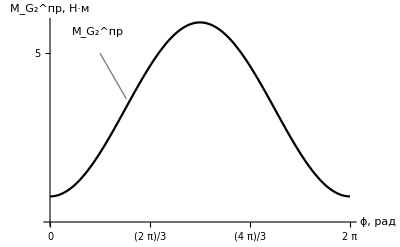

```mathematica
Plot[Callout[MprG2[x],"M_G_2^(:043f:0440)",{Pi/3,5},Appearance->"Line"],{x,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[5i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[5i,{i,-10,12}]},ImageSize->iSize,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesOrigin->{0,-10},AxesLabel->{"ϕ, рад","M_G_2^(:043f:0440), Н·м"}]
```

```mathematica
Ac:=Evaluate[Integrate[Mprsopr[x],{x,0,2Pi}]]
Ac
```

-495.79

```mathematica
Mprdv=-Ac/(2Pi)
```

78.9075

```mathematica
MprS[x_]:=Mprdv+Mprsopr[x]
```

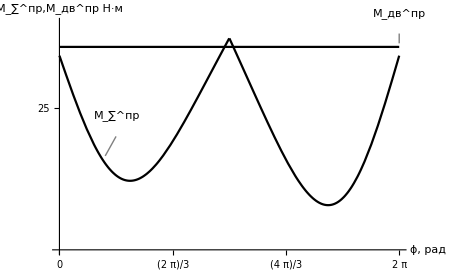

```mathematica
Plot[{Callout[MprS[z],"M_∑^(:043f:0440)",{Pi/3,0},Appearance->"Line"],Callout[Mprdv,"M_(:0434:0432)^(:043f:0440)",Above,Appearance->"Line"]},{z,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize+50,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesOrigin->{0,-100},AxesLabel->{"ϕ, рад","M_∑^(:043f:0440),M_(:0434:0432)^(:043f:0440) Н·м"},PlotRange->100]
```

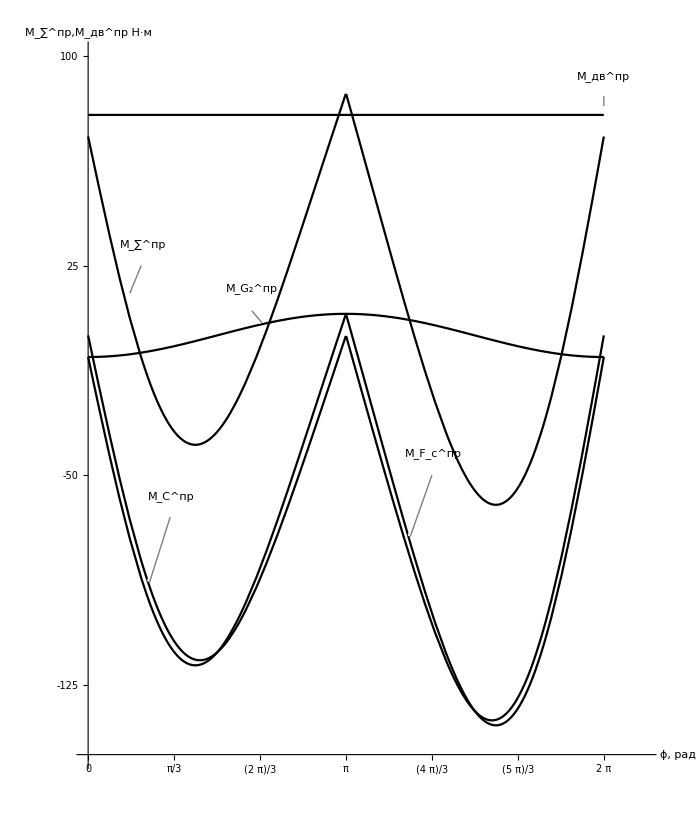

```mathematica
Plot[{Callout[Mprsopr[z],"M_(:0421)^(:043f:0440)",{1,-65},Appearance->"Line"],Callout[Mprc[z],"M_F_c^(:043f:0440)",{4Pi/3,-50},Appearance->"Line"],Callout[MprG2[z],"M_G_2^(:043f:0440)",{2Pi/3-0.1,5},Appearance->"Line"],Callout[MprS[z],"M_∑^(:043f:0440)",{Pi/3-0.4,25},Appearance->"Line"],Callout[Mprdv,"M_(:0434:0432)^(:043f:0440)",Above,Appearance->"Line"]},{z,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->700,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesOrigin->{0,-150},AxesLabel->{"ϕ, рад","M_∑^(:043f:0440),M_(:0434:0432)^(:043f:0440) Н·м"},PlotRange->{{0,2Pi+0.5},{-150,100}},AspectRatio->1.2]
```

```mathematica
Asum[x_]:=Evaluate[Integrate[MprS[z],{z,0,x},Assumptions->x∈Reals]]
Asopr[x_]:=Evaluate[Integrate[Mprsopr[z],{z,0,x},Assumptions->x∈Reals]]
Amg[x_]:=Evaluate[Integrate[MprG2[z],{z,0,x},Assumptions->x∈Reals]]
Adv[x_]:=Evaluate[Integrate[Mprdv,{z,0,x},Assumptions->x∈Reals]]
```

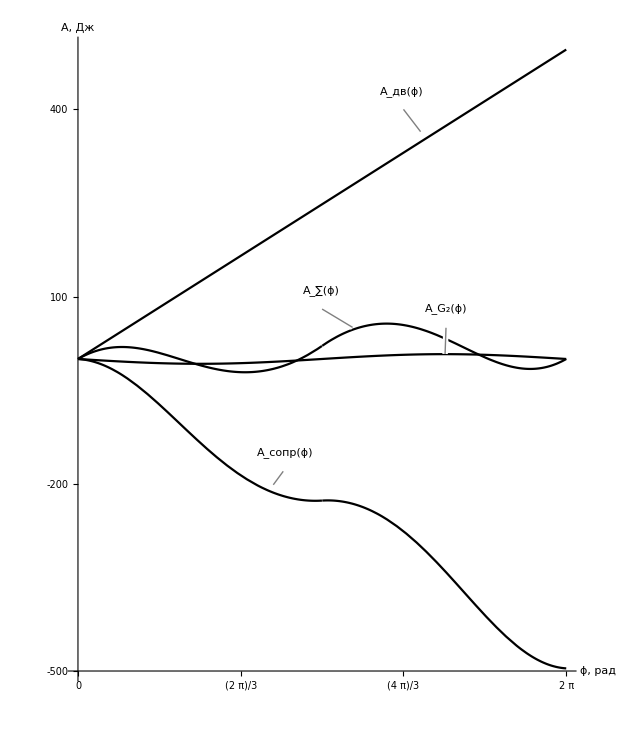

```mathematica
Plot[{Callout[Adv[k],"A_(:0434:0432)(ϕ)",{4Pi/3,400},Appearance->"Line"],Callout[Asum[k],"A_∑(ϕ)",{3Pi/3,80},Appearance->"Line"],Callout[Asopr[k],"A_(:0441:043e:043f:0440)(ϕ)",{3Pi/3-0.5,-180},Appearance->"Line"],Callout[Amg[k],"A_G_2(ϕ)",{5Pi/3-0.5,50},Appearance->"Line"]},{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[100i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[100i,{i,-10,12}]},ImageSize->620,PlotStyle->Black,PlotRange->{500,-510},AxesOrigin->{0,-500},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","A, Дж"},AspectRatio->1.2]
```

```mathematica
Tii[x_]:=JprII[x]w1sr^2/2
```

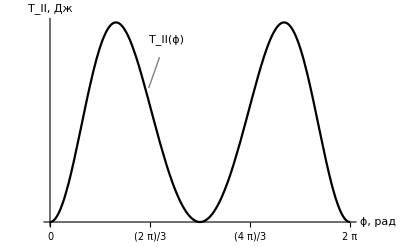

```mathematica
Plot[Callout[Tii[k],"T_II(ϕ)",{2Pi/3+0.2,8},Appearance->"Line"],{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[i,{i,-10,12}]},ImageSize->iSize,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","T_II, Дж"}]
```

```mathematica
dTi[x_]:=Asum[x]-Tii[x]
```

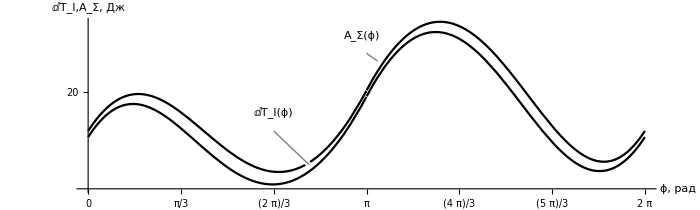

```mathematica
Plot[{Callout[dTi[k],"ⅆT_I(ϕ)",{2Pi/3,0},Appearance->"Line"],Callout[Asum[k],"A_Σ(ϕ)",{3Pi/3,40},Appearance->"Line"]},{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[10i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[10i,{i,-10,12}]},ImageSize->700,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","ⅆT_I,A_Σ, Дж"},AxesOrigin->{0,-30},PlotRange->{{0,2Pi},Automatic},AspectRatio->0.3]
```

```mathematica
Timax=Maximize[{dTi[x],0≤x≤2Pi},x][[1]];
Timin=Minimize[{dTi[x],0≤x≤2Pi},x][[1]];
maxdTi=Timax-Timin
```

79.0649

```mathematica
JprI=maxdTi/(w1sr^2 δ)
```

15.6464

```mathematica
Ti[x_]:=JprI*w1[x]^2/2
```

```mathematica
Ti[3]/w1[3]
```

78.3779

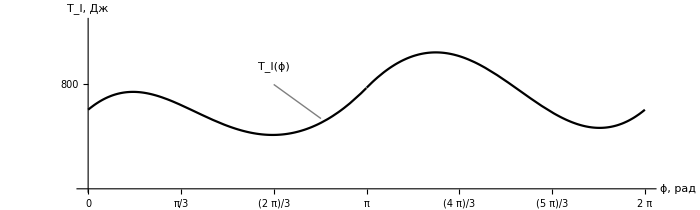

```mathematica
Plot[{Callout[Ti[k],"T_I(ϕ)",{2Pi/3,800},Appearance->"Line"]},{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,120}]},ImageSize->700,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","T_I, Дж"},AxesOrigin->{0,700},PlotRange->{700,860},AspectRatio->0.3]
```

```mathematica
dw1[x_]:=(dTi[x]-(Timax+Timin)/2)/(w1sr JprI)
w1sr1[k_]:=RandomReal[{w1sr-0.00001,w1sr+0.00001}]
w1[x_]:=w1sr+dw1[x]
```

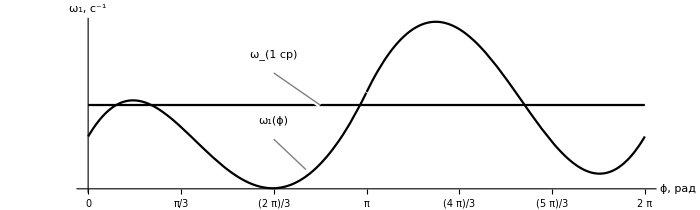

```mathematica
Plot[{Callout[w1sr1[k],"ω_(1 :0441:0440)",{2Pi/3,10.15},Appearance->"Line"],Callout[w1[k],"ω_1(ϕ)",{2Pi/3,10-0.05},Appearance->"Line"]},{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-8,120}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[.10i,{i,-10,120}]},ImageSize->700,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","ω_1, (:0441)^-1"},AxesOrigin->{0,9.8},AspectRatio->0.3]
```

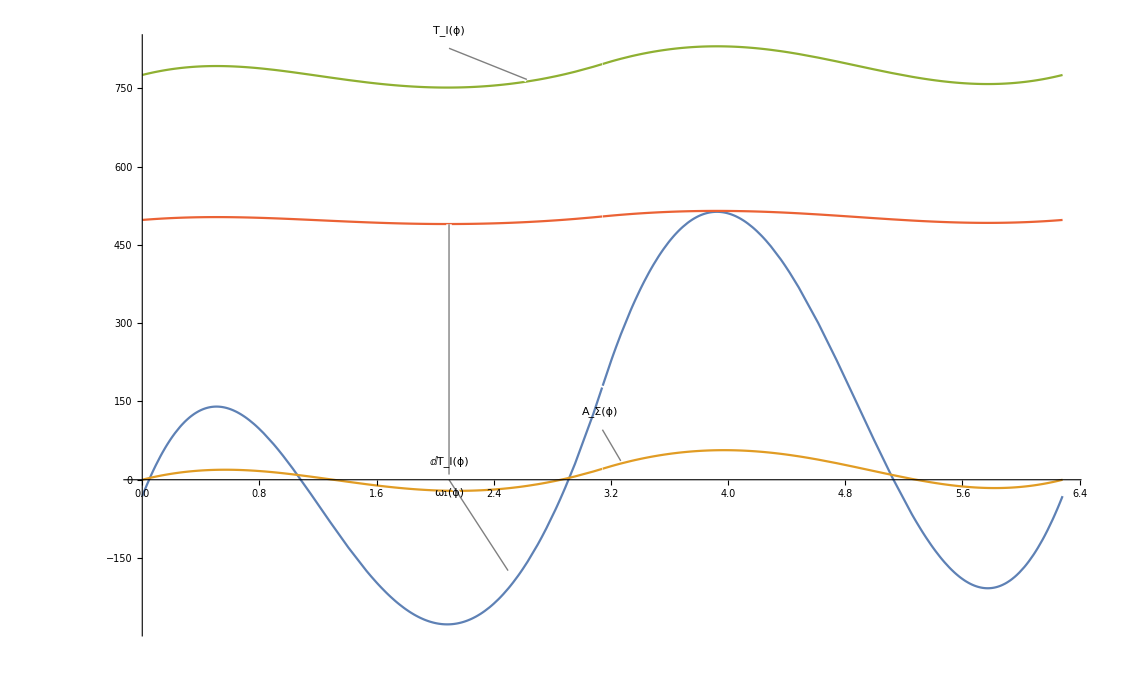

```mathematica
Plot[{Callout[10dTi[k],"ⅆT_I(ϕ)",{2Pi/3,0},Appearance->"Line"],Callout[Asum[k],"A_Σ(ϕ)",{3Pi/3,40},Appearance->"Line"],Callout[Ti[k],"T_I(ϕ)",{2Pi/3,800},Appearance->"Line"],Callout[50w1[k],"ω_1(ϕ)",{2Pi/3,10-0.05},Appearance->"Line"]},{k,0,2Pi}]
```

```mathematica
ϵ[x_]:=MprS[x]/(JprII[x]+JprI)-w1[x]^2/(2(JprII[x]+JprI))D[JprII[z],z]/.z->x
```

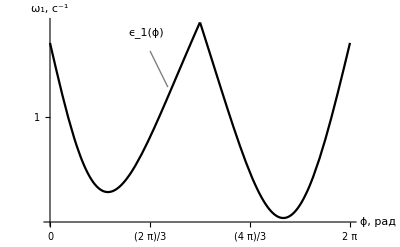

```mathematica
Plot[{Callout[ϵ[k],"ϵ_1(ϕ)",{2Pi/3,4.15},Appearance->"Line"]},{k,0,2Pi},Ticks->{Table[Pi /3i,{i,0,8}],Table[1i,{i,-8,120}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[1i,{i,-10,120}]},ImageSize->iSize,PlotStyle->Black,AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},AxesLabel->{"ϕ, рад","ω_1, (:0441)^-1"},AxesOrigin->{0,-4}]
```